```mathematica
V={1,2,3}
```

{1,2,3}

```mathematica
A={{1,2,3},{4,5,6},{0,34,1},{14,1,12}}
```

{{1,2,3},{4,5,6},{0,34,1},{14,1,12}}

```mathematica
MatrixForm[A]
```

(1 | 2 | 3
4 | 5 | 6
0 | 34 | 1
14 | 1 | 12)

```mathematica
VectorQ[V]
```

True

```mathematica
A[[1,3]]
```

3

```mathematica
P = {{1,3,4},{1,2,3},{3,12,1/2}}
```

{{1,3,4},{1,2,3},{3,12,1/2}}

```mathematica
MatrixForm[MatrixPower[P, 3]]
```

(118 | 342 | 485/2
179/2 | 260 | 731/4
801/4 | 1413/2 | 1657/8)

```mathematica
Dimensions[A]
```

{4,3}

```mathematica
Dimensions[A][[1]]
```

4

```mathematica
Dimensions[A][[2]]
```

3

```mathematica
B={{a,b,c,d},{1,2,3,4},{2,2,7,5},{4,9,10,0}}
```

{{a,b,c,d},{1,2,3,4},{2,2,7,5},{4,9,10,0}}

```mathematica
Det[B]
```

-137 a+22 b+35 c-3 d

```mathematica
MatrixForm[Inverse[B]]
```

(-137/(-137 a+22 b+35 c-3 d) | (50 b-45 c+43 d)/(-137 a+22 b+35 c-3 d) | (-40 b+36 c-7 d)/(-137 a+22 b+35 c-3 d) | (13 b+2 c-8 d)/(-137 a+22 b+35 c-3 d)
22/(-137 a+22 b+35 c-3 d) | (-50 a+20 c-8 d)/(-137 a+22 b+35 c-3 d) | (40 a-16 c+2 d)/(-137 a+22 b+35 c-3 d) | (-13 a+3 c+d)/(-137 a+22 b+35 c-3 d)
35/(-137 a+22 b+35 c-3 d) | (45 a-20 b-10 d)/(-137 a+22 b+35 c-3 d) | (-36 a+16 b+d)/(-137 a+22 b+35 c-3 d) | (-2 a-3 b+2 d)/(-137 a+22 b+35 c-3 d)
-3/(-137 a+22 b+35 c-3 d) | (-43 a+8 b+10 c)/(-137 a+22 b+35 c-3 d) | (7 a-2 b-c)/(-137 a+22 b+35 c-3 d) | (8 a-b-2 c)/(-137 a+22 b+35 c-3 d))

```mathematica
MatC={{1,3},{2,7}}
```

{{1,3},{2,7}}

```mathematica
MatrixPower[MatC, -1] // MatrixForm
```

(7 | -3
-2 | 1)

```mathematica
Inverse[MatC] // MatrixForm
```

(7 | -3
-2 | 1)

```mathematica
x1= {xa1,xa2,xa3, xa4}
```

{xa1,xa2,xa3,xa4}

```mathematica
x2={xb1,xb2,xb3,xb4}
```

{xb1,xb2,xb3,xb4}

```mathematica
x1*x2
```

{xa1 xb1,xa2 xb2,xa3 xb3,xa4 xb4}

```mathematica
Cross[{ya1,ya2,ya3},{yb1,yb2,yb3}]
```

{-ya3 yb2+ya2 yb3,ya3 yb1-ya1 yb3,-ya2 yb1+ya1 yb2}

```mathematica
x1[[2]]=0
```

0

```mathematica
x1
```

{xa1,0,xa3,xa4}

```mathematica
Length [x1]
```

4

```mathematica
Length [A]
```

4

```mathematica
ContourPlot3D[x^2-y^2 -z ==0, {x, -10, 10 },{y,-10,10 },{z, -10,10}]
```

-Graphics3D-

ContourPlot::nonopt: Options expected (instead of {z,-10,10}) beyond position 3 in ContourPlot[x^2-y^2-z==0,{x,-10,10},{y,-10,10},{z,-10,10}]. An option must be a rule or a list of rules.

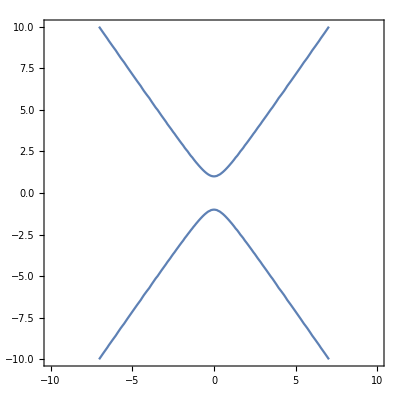

```mathematica
ContourPlot[2x^2 - y^2 == -1, {x,-10,10},{y,-10,10}, Axes->{True,True}]
```

```mathematica
Transpose[A] // MatrixForm
```

(1 | 4 | 0 | 14
2 | 5 | 34 | 1
3 | 6 | 1 | 12)

```mathematica
RowReduce[Transpose[A]] // MatrixForm
```

(1 | 0 | 0 | -386/67
0 | 1 | 0 | 331/67
0 | 0 | 1 | -24/67)

```mathematica
SashaMat=DiagonalMatrix[x1]
```

{{xa1,0,0,0},{0,xa2,0,0},{0,0,xa3,0},{0,0,0,xa4}}

```mathematica
MatrixPower[SashaMat, -1] // MatrixForm
```

(1/xa1 | 0 | 0 | 0
0 | 1/xa2 | 0 | 0
0 | 0 | 1/xa3 | 0
0 | 0 | 0 | 1/xa4)

```mathematica
Inverse[SashaMat] // MatrixForm
```

(1/xa1 | 0 | 0 | 0
0 | 1/xa2 | 0 | 0
0 | 0 | 1/xa3 | 0
0 | 0 | 0 | 1/xa4)

```mathematica
m1= {1,2,3}
```

{1,2,3}

```mathematica
m2 = {4,3,2}
```

{4,3,2}

```mathematica
m3={69069, 15, 78}
```

{69069,15,78}

```mathematica
Cross[m1,m2]*m3
```

{-345345,150,-390}

```mathematica
Manipulate[ContourPlot3D[{x^2-y^2-z==0, x^2+y^2+(z-h)^2==4}, {x, -10, 10},{y, -10, 10},{z, -10, 10}, ContourStyle->{{Green, Mesh->None},{Orange}}],{h, -10, 10}]
```